In the present file we develop and write matrices corresponding to 1D moment systems.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_1D

## develop sparsity and write matrix

Use this function to create the entries of the sparse matrix. The first value written to the file is the number of non zeros. Incase of symbolic matrices, the entries are considered to be 1. flag = 0 for symbolic, flag = 1 for constant matrices.

1) flag = 0: in the case one only needs the location of the non zeros entries
2) flag = 1; in the case when one also needs the values of the entries

Caution: always send N[a].
CAUTION: not be used for symbolic matrices

```mathematica
developsparsity2[a_,filename_]:=Module[{nnz,indicies,rowindicies,colindicies,entries,str,numzeros,rows,cols},

(*total number of non-zeros in the matrix*)
indicies = ArrayRules[a][[1;;-2]];
rows = Length[a];
cols = Length[a⟦1⟧];

nnz = Length[indicies];
rowindicies = ConstantArray[0,Length[indicies]];
colindicies = ConstantArray[0,Length[indicies]];
entries = ConstantArray[0,Length[indicies]];

Do[rowindicies[[ii]]=indicies[[ii]][[1]][[1]],{ii,1,Length[indicies]}];

Do[colindicies[[ii]]=indicies[[ii]][[1]][[2]],{ii,1,Length[indicies]}];

Do[entries[[ii]]=indicies[[ii]][[2]],{ii,1,Length[indicies]}];

str = OpenWrite[StringJoin["system_matrices1D/",filename]];

Print[Style[StringJoin["/system_matrices1D/",filename],FontColor->Green]];
WriteString[str,StringJoin[ToString[rows]," ",ToString[cols]],"\n"];

Do[WriteString[str,ToString[rowindicies[[ii]]]," " ,ToString[colindicies[[ii]]]," " ,ToString[entries[[ii]]],"\n"],{ii,1,Length[rowindicies]}];

Close[str];

]

(*write a vector to a file*)
writeVector[vec_,filename_]:=Module[{NumEntries,str,destination},

(*first we write the number of entries in the vector*)
NumEntries = Length[vec];

destination = StringJoin["../system_matrices/",filename];

(*first open the file to write*)
str = OpenWrite[destination];

(*first write the number of entries to the file*)
WriteString[str,ToString[NumEntries],"\n"];

(*write the vector to the opened file*)
(*The care regarding C indices has already been taken off in the main routine*)
Do[WriteString[str,ToString[vec[[ii]]],"\n"],{ii,1,Length[vec]}];

Close[str];

]
```

## Some Testing with Hermite Functions (normalized)

```mathematica
Clear[f0]
```

```mathematica
f0[c_]=1/(√(2π))Exp[-c^2/2];
fM[c_]=(c v-θ/2+(c^2 θ)/2+ρ)f0[c];
H[i_,c_]=1/(√Gamma[i+1] 2^(i/2))HermiteH[i,c/√2];

(*Distribution with respect to L2*)
H2[i_,c_]=1/(√Gamma[i+1] 2^(i/2))HermiteH[i,c];
fG[c_,n_]:=∑_(k=0)^(n-1) α[k]H[k,c]f0[c];

(*The integrand part of f, to be only used for numerical integration*)
fIntegrand[c_,n_]:=1/(√(2π))(∑_(k=0)^(n-1) α[k]H2[k,c]);

(*The following routine integrates the following expressions ∫_0^∞ H[n,c]H[m,c]f0[c]ⅆc *)
```

```mathematica
HSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(n!m!))/(n!)(∑_(i=1)^n (2^(1/2 (1-2 i+m+n)) π)/(Gamma[(i-m)/2] Gamma[2-i+m] Gamma[1/2 (1+i-n)])+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];

(*Simplified expression for half space integral *)
ExplicitHSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(m!))/(√(n!))(∑_(p=1)^n 1/((p-m-2)!! (1-p+m)! (p-n-1)!!)+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];
```

### Permutation matrix

```mathematica
(*Returns a transformation matrix from var2 to var1 i.e. var1=Perm v2*)
PermuteVar[var1_,var2_]:=Module[{result,nEqn,pos},

nEqn = Length[var1];
result = ConstantArray[0,{nEqn,nEqn}];

Do[pos = Flatten[Position[var2,var1[[ii]]]];
result⟦ii,pos⟧=1,{ii,1,nEqn}];

result

]
```

## Equations for α_j, incl. Eigenvalues

(0 | 1 | 0 | 0
1 | 0 | √2 | 0
0 | √2 | 0 | √3
0 | 0 | √3 | 0)

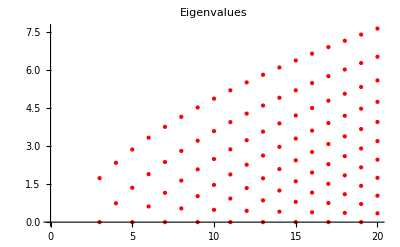

```mathematica
AA[n_]:=Table[If[i==j+1,√i,If[i==j-1,√(i+1),0]],{i,0,n-1},{j,0,n-1}];

MatrixForm[AA[4]]
ListPlot[N[Table[Thread[{Table[n,{i,1,If[OddQ[n],(n)/2+1,(n)/2]}],N[Select[Eigenvalues[AA[n]],#≥0&]]}],{n,3,20}]],PlotLabel->"Eigenvalues",PlotStyle->{{Red,Thick,PointSize[Large]}}]
```

## Boundary Matrices

```mathematica
Clear[MatBoe]
```

### Mat Aoe

```mathematica
(*construct Aoe*)
MatAoe[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=ConstantArray[0,{Length[IDOdd],Length[IDEven]}];
Do[Do[If[ii==jj,result⟦ii,jj⟧=Sqrt[IDOdd⟦ii⟧],If[jj==ii+1,result⟦ii,jj⟧=Sqrt[IDOdd⟦ii⟧+1]]],{jj,1,Length[IDEven]}],{ii,1,Length[IDOdd]}];

result

]
```

### Mat Boe

```mathematica
(*With the assumption that the normal points from the gas into the wall.*)
MatBoe[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven,rhoW},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=Flatten[ConstantArray[0,{Length[IDOdd],1}]];


(*First we compute the density at the wall*)
rhoW=Expand[ρW/.Solve[(Expand[(ρW HSpcInt[1,0]+0 HSpcInt[1,1]+θW/√2 HSpcInt[1,2])-∑_(j=0)^((n-1)/2) α[2j]HSpcInt[1,2j]])==0,ρW]⟦1⟧];


(*2 comes from the left hand side of the boundary conditions and the minus comes from the direction of the normal. α[2] = θW/(√2)*)
Do[result⟦ii⟧=-2((rhoW HSpcInt[IDOdd⟦ii⟧,0]+0 HSpcInt[IDOdd⟦ii⟧,1]+θW/√2 HSpcInt[IDOdd⟦ii⟧,2])-∑_(j=0)^((n-1)/2) α[2j]HSpcInt[IDOdd⟦ii⟧,2j]),{ii,1,Length[IDOdd]}];

CoefficientArrays[result,Map[α[#]&,IDEven]]⟦2⟧
]

(*Boe matrix for the inflow boundary conditions.*)
MatBoeInflow[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven,rhoW},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=Flatten[ConstantArray[0,{Length[IDOdd],1}]];

(*2 comes from the left hand side of the boundary conditions and the minus comes from the direction of the normal. α[2] = θW/(√2)*)
Do[result⟦ii⟧=2(∑_(j=0)^((n-1)/2) α[2j]HSpcInt[IDOdd⟦ii⟧,2j]),{ii,1,Length[IDOdd]}];

CoefficientArrays[result,Map[α[#]&,IDEven]]⟦2⟧
]
```

### Mat Onsager

```mathematica
MatOnsager[n_]:=Module[{Btilde,result},

(*Following the notation in the boundary condition paper, this is \hat{M}^(mbc)*)
Btilde=MatBoe[n]⟦1;;-1,1;;Length[MatBoe[n]]⟧;

(*We now develop the Onsager matrix using the Maxwell's accommodation model*)
Btilde.Inverse[MatAoe[n]⟦1;;-1,1;;Length[MatAoe[n]]⟧]
]

MatOnsagerInflow[n_]:=Module[{Btilde,result,Boe,Aoe},
Boe = MatBoeInflow[n];
Aoe = MatAoe[n];

(*Following the notation in the boundary condition paper, this is \hat{M}^(mbc)*)
Btilde=Boe⟦All,1;;Length[Boe]⟧;

Btilde.Inverse[Aoe⟦All,1;;Length[Aoe]⟧]
]
```

## Final Matrices

### Permutation matrix

```mathematica
(*Returns a transformation matrix from var2 to var1 i.e. var1=Perm v2*)
PermuteVar[var1_,var2_]:=Module[{result,nEqn,pos},

nEqn = Length[var1];
result = ConstantArray[0,{nEqn,nEqn}];

Do[pos = Flatten[Position[var2,var1[[ii]]]];
result⟦ii,pos⟧=1,{ii,1,nEqn}];

result

]
```

### Checks for properties of a matrix

```mathematica
CheckSPD[Mat_,matrixname_]:=Module[{entries,error,EV,$MaxExtraPrecision=150},

Print[Style[matrixname,FontColor->Magenta]];
entries=Length[Flatten[Mat]];
error=Chop[Simplify[Mat-Transpose[Mat]]];
EV=Chop[N[Eigenvalues[N[Mat]]]];

(*check for the symmetricity of the matrices by computing A - Transpose[A]*)
If[Count[Flatten[error],0]≠entries,Print[Style["Not Symmetric",FontColor->Red]],Print[Style["Symmetric",FontColor->Green]]];

(*compute the positive definetness by computing the eigenvalues*)
If[Length[Select[EV,#<=0&]]>0,Print[Style["Negative Definite",FontColor->Red]],Print[Style["Positive Definite",FontColor->Green]]];
]

CheckSSPD[Mat_,matrixname_]:=Module[{entries,error,EV,$MaxExtraPrecision=150},

Print[Style[matrixname,FontColor->Magenta]];
entries=Length[Flatten[Mat]];
error=Chop[Simplify[Mat-Transpose[Mat]]];
EV=Chop[N[Eigenvalues[N[Mat]]]];

(*check for the symmetricity of the matrices by computing A - Transpose[A]*)
If[Count[Flatten[error],0]≠entries,Print[Style["Not Symmetric",FontColor->Red]],Print[Style["Symmetric",FontColor->Green]]];

(*compute the positive definetness by computing the eigenvalues*)
If[Length[Select[EV,#<0&]]>0,Print[Style["Negative Definite",FontColor->Red]],Print[Style["Positive Semi-Definite",FontColor->Green]]];
]
```

### Core Routine

```mathematica
Clear[α]
```

```mathematica
FinalMatrices1D[Ntensors_]:=Module[{Ax,Boe,var,varRearranged,IDEven,IDOdd,OddVar,EvenVar,B,PermuteMat,PermuteMatInv,Sigma,nEqn,nBC,OnsagerMat,OnsagerMatInflow,BoeInflow,BInflow,filenameAx,filenameB,filenameBinflow,$MaxExtraPrecision=150,precision = 15},

Ax = AA[Ntensors];

(*Develop all the variables needed by the present routine*)
var = Map[α[#]&,Range[0,Ntensors-1,1]];(*total number of variables = Ntensors*)
IDOdd =Range[2,Ntensors,2]; (*ID of the odd variables.*)
IDEven = Range[1,Ntensors,2];

(*Computation of the Onsager matrix along with the fix for the normal velocity. *)
(*OnsagerMat = MatOnsager[Ntensors];
OnsagerMatInflow = MatOnsagerInflow[Ntensors];*)

(*boundary conditions of the form Uo = Boe*Ue. From the Maxwell's accommodatio model. *)
(*Boe = OnsagerMat.MatAoe[Ntensors];
BoeInflow = OnsagerMatInflow.MatAoe[Ntensors];*)

(*Boe = MatBoe[Ntensors];*)
BoeInflow=MatBoeInflow[Ntensors];

(*B = ConstantArray[0,{Length[IDOdd],Ntensors}];
B⟦All,IDOdd⟧ = IdentityMatrix[Length[IDOdd]];
B⟦All,IDEven⟧ = - Boe;*)

BInflow = ConstantArray[0,{Length[IDOdd],Ntensors}];
BInflow⟦All,IDOdd⟧ = IdentityMatrix[Length[IDOdd]];
BInflow⟦All,IDEven⟧ = - BoeInflow;

filenameBinflow = StringJoin["Binflow_1D_",ToString[Ntensors],".txt"];
filenameB = StringJoin["Bwall_1D_",ToString[Ntensors],".txt"];
filenameAx = StringJoin["A1_1D_",ToString[Ntensors],".txt"];


(*developsparsity2[N[B,precision],filenameB];*)

developsparsity2[N[BInflow,precision],filenameBinflow];
developsparsity2[N[Ax,precision],filenameAx];

]
```

## Results

### All Systems

```mathematica
Do[FinalMatrices1D[ii],{ii,21,150}]
```

/system_matrices1D/Binflow_1D_21.txt

/system_matrices1D/A1_1D_21.txt

/system_matrices1D/Binflow_1D_22.txt

/system_matrices1D/A1_1D_22.txt

/system_matrices1D/Binflow_1D_23.txt

/system_matrices1D/A1_1D_23.txt

/system_matrices1D/Binflow_1D_24.txt

/system_matrices1D/A1_1D_24.txt

/system_matrices1D/Binflow_1D_25.txt

/system_matrices1D/A1_1D_25.txt

/system_matrices1D/Binflow_1D_26.txt

/system_matrices1D/A1_1D_26.txt

/system_matrices1D/Binflow_1D_27.txt

/system_matrices1D/A1_1D_27.txt

/system_matrices1D/Binflow_1D_28.txt

/system_matrices1D/A1_1D_28.txt

/system_matrices1D/Binflow_1D_29.txt

/system_matrices1D/A1_1D_29.txt

/system_matrices1D/Binflow_1D_30.txt

/system_matrices1D/A1_1D_30.txt

/system_matrices1D/Binflow_1D_31.txt

/system_matrices1D/A1_1D_31.txt

/system_matrices1D/Binflow_1D_32.txt

/system_matrices1D/A1_1D_32.txt

/system_matrices1D/Binflow_1D_33.txt

/system_matrices1D/A1_1D_33.txt

/system_matrices1D/Binflow_1D_34.txt

/system_matrices1D/A1_1D_34.txt

/system_matrices1D/Binflow_1D_35.txt

/system_matrices1D/A1_1D_35.txt

/system_matrices1D/Binflow_1D_36.txt

/system_matrices1D/A1_1D_36.txt

$Aborted

```mathematica
FinalMatrices1D[199]
```

/system_matrices1D/Binflow_1D_199.txt

/system_matrices1D/A1_1D_199.txt

## Manufactured Solutions

```mathematica
ManufacturedSolution:=Module[{Ax,B2,B1,g2,g1,sol,force,P,Kn,IDOdd},
sol = Table[Sin[(π x)/ii]Cos[(π t)/ii],{ii,1,4}];
Kn = 1;

{Ax,B2}=FinalMatrices1D[4];
IDOdd = {2,4};
B1 =B2;
B1⟦All,IDOdd⟧=-B1⟦All,IDOdd⟧;

P = ConstantArray[0,{4,4}];
P⟦-1,-1⟧=-1/Kn;

force = D[sol,t]+Ax.D[sol,x]-P.sol;

g2 = Expand[B2.sol];
g1 = Expand[B1.sol];

{sol/.t->0,force,g2,g1}

]
```

```mathematica
trialsource=ManufacturedSolution⟦2⟧;
```

```mathematica
CForm[trialsource⟦4⟧]/.{Pi->pi,Cos->cos,Sin->sin}
```

(pi*cos((pi*t)/3.)*cos((pi*x)/3.))/Sqrt(3) + cos((pi*t)/4.)*sin((pi*x)/4.) - 
   (pi*sin((pi*t)/4.)*sin((pi*x)/4.))/4.

## Norms of matrices

```mathematica
NormAoeR = Table[Norm[N[MatOnsagerInflow[ii].MatAoe[ii]⟦All,-1⟧-MatBoeInflow[ii]⟦All,-1⟧],2],{ii,5,30,2}];
```

```mathematica
NormAoeR
```

{0.879585,1.13392,1.35255,1.54701,1.72373,1.88673,2.03873,2.18165,2.31692,2.44562,2.56861,2.68658,2.80009}

```mathematica
Log[NormAoeR⟦-1⟧/NormAoeR⟦-2⟧]/Log[29/27]
```

0.579094